```mathematica
Needs["NeffConstraint`"]
```

### Analytic preliminaries

#### LIPS out of COM

```mathematica
Clear[M2]
dΠLIPS=dΩ/(16 π^2) kD/Ei /.Ei ->p + mD
dΠi = (nD g)/(mD p)     (dp  p^2)/(8 π^2)1/(E^(β p)+1)
Integrand = Simplify[Simplify[dΠLIPS dΠi M2 Et]]
```

(dΩ kD)/(16 (mD+p) π^2)

(dp g nD p)/(8 (1+ⅇ^(p β)) mD π^2)

(d^2 dp dΩ g kD M2 nD p^3)/(64 (1+ⅇ^(p β)) (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

Mandelstam variables

```mathematica
s = Simplify[(mD + p)^2 - p^2]
t = Simplify[(Et)^2 - q^2]
u = FullSimplify[(Ef - mD)^2-Ef^2]
```

mD (mD+2 p)

-(4 d^2 mD^2 p^2)/(mD^2+2 mD p-(-1+d^2) p^2)

(mD (mD^3+3 (-1+d^2) mD p^2+2 (-1+d^2) p^3))/((mD+p-d p) (mD+p+d p))

```mathematica
Et
```

(2 d^2 mD p^2)/(-d^2 p^2+(mD+p)^2)

```mathematica
M2lD =FullSimplify[(8 e^2 eD^2 ϵ^2)/t^2((s/2)^2+(u/2)^2)] (*lepton dark matter scattering*)
```

1/(4 d^4 mD^2 p^4)e^2 eD^2 (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2

```mathematica
Integrand/.M2->M2lD
```

(dp dΩ e^2 eD^2 g kD nD (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2)/(256 d^2 (1+ⅇ^(p β)) mD^2 p (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

```mathematica
Integrate[Integrand,d]
```

(dp dΩ g kD M2 nD (-2 d p-(mD+p) Log[-mD+(-1+d) p]+(mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) (mD+p) π^4)

```mathematica
Simplify[2 π/dΩ Integrate[Integrand/.M2->M2lD,d]]
FullSimplify[((%/.d->1)-(%/.d->-1))/mD^2]
```

(dp e^2 eD^2 g kD nD ϵ^2 (-((mD+p)^2 (mD^2+4 p^2))/d-d p^2 (5 mD^2+8 mD p+4 p^2)-4 mD^2 p (mD+p) Log[mD+p-d p]+4 mD^2 p (mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) mD^2 p (mD+p) π^3)

-((dp e^2 eD^2 g kD nD ϵ^2 (mD^4+2 mD^3 p+10 mD^2 p^2+16 mD p^3+8 p^4+4 mD^2 p (mD+p) (Log[mD]-Log[mD+2 p])))/(64 (1+ⅇ^(p β)) mD^4 p (mD+p) π^3))

#### Massive case - in momentum variables

compute q and compare to massless case

```mathematica
Clear[θsol,d]
θsol = Solve[mD + √(p^2+m^2) == √(mD^2 + kD^2) + √(p^2 - 2 p d kD + kD^2 + m^2),d][[1]]
d= Simplify[d/.θsol]
PowerExpand[Series[d,{kD,0,1}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{d→(-mD^2+mD √(kD^2+mD^2)-mD √(m^2+p^2)+√(kD^2+mD^2) √(m^2+p^2))/(kD p)}

((-mD+√(kD^2+mD^2)) (mD+√(m^2+p^2)))/(kD p)

((mD+√(m^2+p^2)) kD)/(2 mD p)+O[kD]^2

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

Compute E transfered

```mathematica
(*Ef = FullSimplify[√(p^2 - 2 kD d p +kD^2+m^2)/.θsol]*)
Ef = FullSimplify[mD +√(p^2+m^2) - √(mD^2 + kD^2)]
Et =FullSimplify[√(mD^2 + kD^2)-mD]
ESM = √(p^2+m^2)
Ei = ESM + mD
```

mD-√(kD^2+mD^2)+√(m^2+p^2)

-mD+√(kD^2+mD^2)

√(m^2+p^2)

mD+√(m^2+p^2)

```mathematica
Simplify[Expand[(ESMt + mD)^2/(ESMt^2-m^2) -1]]
```

(m^2+2 ESMt mD+mD^2)/(ESMt^2-m^2)

```mathematica
s=Simplify[(mD + ESM)^2-p^2] (*p + pD squared*)
t = Simplify[ (Et)^2- kD^2](*kD - pD squared*)
(*u = Simplify[(Ef-mD)^2-√(Ef^2-m^2)](*k - pD squared*)*)
u = Simplify[(Ef-mD)^2-(Ef^2-m^2)](*k - pD squared*)
```

m^2+mD (mD+2 √(m^2+p^2))

2 mD (mD-√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2-mD^2+2mD Ei](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+3mD^2+2mD (Et-Ei)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2+mD^2+2mD ESM](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+mD^2+2mD (Et-ESM)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[u+t+s]
```

2 (m^2+mD^2)

### Analyze Cosmology of aDM between recombination and annihilation

```mathematica
CosmoParams[]
```

{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}

#### Initialize

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.72523×10^16 and 8.434×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.24981×10^16 and 1.72128×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.18099×10^17 and 1.94891×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

#### Plot hubble and aH

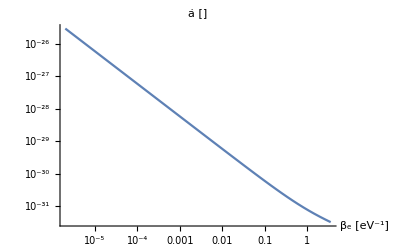

```mathematica
LogLogPlot[aH[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

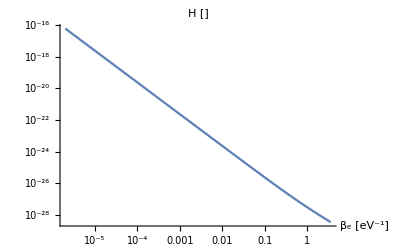

```mathematica
LogLogPlot[H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"H []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

#### Screening length comparison and Expected rate scaling

Λ and 1/(Z_1 β ȧ) control the scaling of the rate

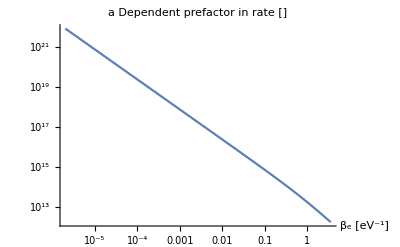

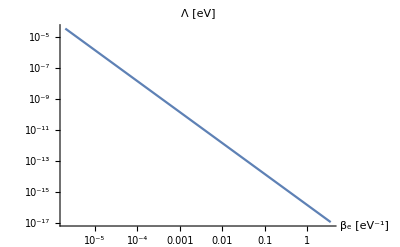

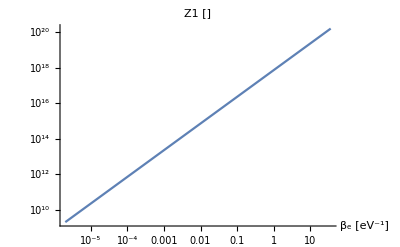

```mathematica
LogLogPlot[1/(Z1[β] aH[β]β)/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"a Dependent prefactor in rate []",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Λ[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Z1[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],10/("TR")/.CosmoParams[]},PlotLabel->"Z1 []",AxesLabel->{"β_e [eV^-1]"}]
```

So it seems like partition function dominates over temperature scaling of a, and the reduced screening at late times.

```mathematica
Z1[1/("Td")]/.CosmoParams[]
```

2.00913×10^9

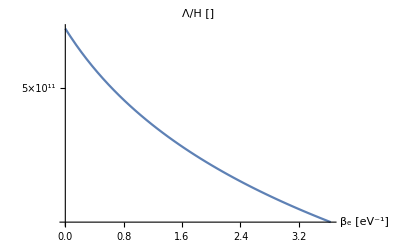

```mathematica
LogPlot[Λ[β]/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

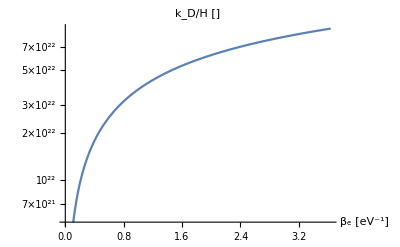

```mathematica
LogPlot[(√(2 "me" Λ[β]))/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

#### Rate and Energy plots - SM aDM mass values

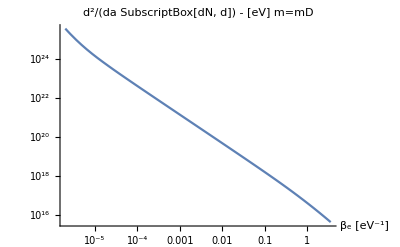

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

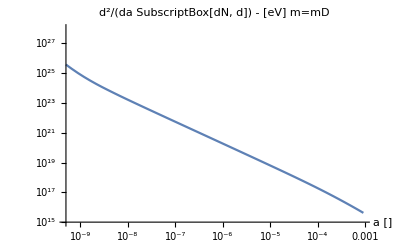

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

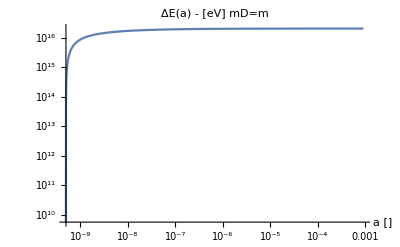

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

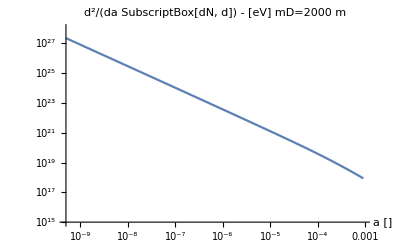

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

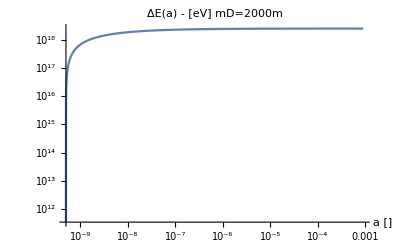

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

#### Neff constraint

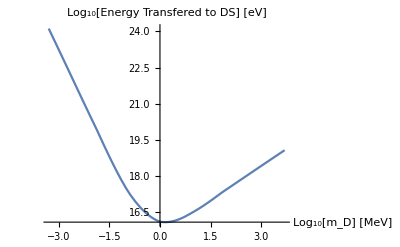

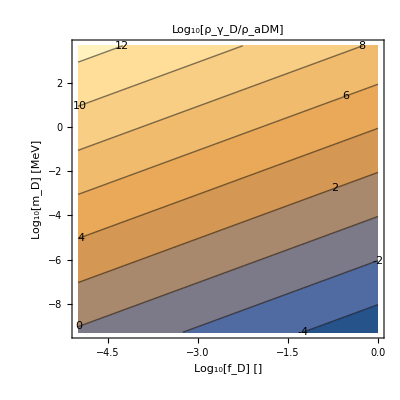

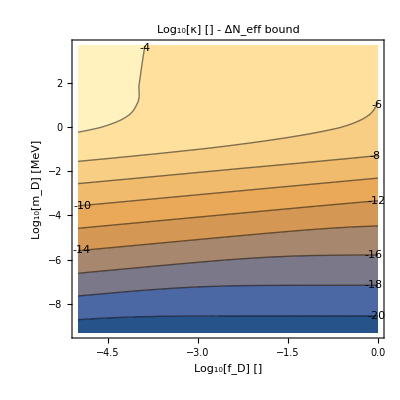

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

#### Interaction Rate - IR domination Debugging

```mathematica
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ,params_,l_:1]:= Module[{Integrand},
(*l - == 1 => energy transfer rate integrand, == 0 => interaction rate (over Subscript[n, D]) integrand*)
 Integrate[Ett^l/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett];
	Simplify[%/."ms"->("m"^2+"mD"^2)/(2 "mD")];
	Integrand =Simplify[Simplify[(%/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(%/.Ett->0)]];
2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"]^l Integrand /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params
]*)
```

```mathematica
(*ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ,params_]:=(m/.params)/ξβ NIntegrate[ NumIntegrand[mD,m,κ,ξβ,ξE,params],{ξE,0,∞}](*extra factor comes from jacobian*)*)
```

```mathematica
inter1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

```mathematica
interrate1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

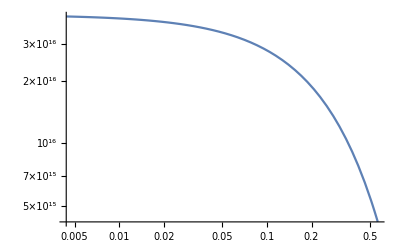

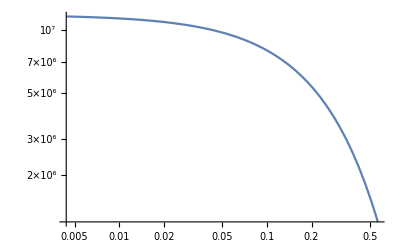

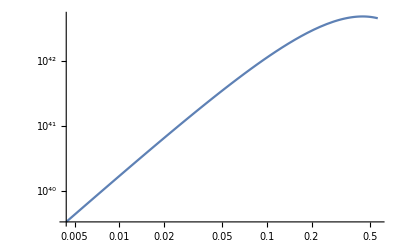

```mathematica
LogLogPlot[10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[nDR[10^-2,interrate1me[["mD"]]]10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[(10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]])/H[β]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
```

```mathematica
nDR[10^-2,10^6]/.CosmoParams[]
```

1.42034×10^-10

```mathematica
Plot[NeffConstraint`ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,ξβ,CosmoParams[],1],{ξβ,1,10^6}]
```

$Aborted

```mathematica
?ESMIntegral
```

```mathematica
?NumIntegrand
```

```mathematica
NeffConstraint`NumIntegrand["me"/.CosmoParams[],"me"/.CosmoParams[],1,10^5,10^-5,CosmoParams[],0]
```

0.293113

```mathematica
Block[{l=1,Integrand,params=CosmoParams[],v1,v2,v3},
v1=Simplify[Integrate[Ett^l/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett]];
	v2=Simplify[v1/."ms"->("m"^2+"mD"^2)/(2 "mD")];
	v3 =Simplify[Simplify[(v2/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(v2/.Ett->0)]];
Integrand=2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"]^l v3 /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params;
(*Print[v1];
Print[v2];*)
(*Print[Integrand];*)
Print[Integrand/.{"m"->"me"/.CosmoParams[],"mD"->"me"/.CosmoParams[],"κ"->1}/.CosmoParams[]]
]
```

(8.95453×10^31 ⅇ^(-((mt+(mt ξE)/ξβ) ξβ)/mt+(ξβ (mt-(mt Log[(7.10335×10^17)/(mt/ξβ)^(3/2)])/ξβ))/mt) mt κ^2 (-((mDt^2+mt^2)^2)/(2 mDt^2)+(2 (mt^2+mDt (mDt-2 (mt+(mt ξE)/ξβ)-(2.91415×10^-16 mt^2)/ξβ^2)) (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(2 mDt^2)/((-1+(mDt+mt+(mt ξE)/ξβ)^2/(-mt^2+(mt+(mt ξE)/ξβ)^2))^2)-2 (mt+(mt ξE)/ξβ)^2-(2.12306×10^-32 mt^4)/ξβ^4+(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(1.45707×10^-16 mt^2 (((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(2.12306×10^-32 mt^4)/ξβ^4-(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2))/(((2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2) ξβ^2)-(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2+(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2]-(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(1.45707×10^-16 mt^2)/ξβ^2]))/(mDt √(0.68+(2.4064×10^10 mt^4)/ξβ^4+(2.048×10^10 mt^3)/ξβ^3+(160000. mt^2)/ξβ^2) ξβ)

```mathematica
-2 ("ESMt"-"ms"+"Λ") Ett+Ett^2/2+("Λ" (2 ("ESMt")^2+2 ("ms")^2+2 "ESMt" "Λ"-2 "ms" "Λ"+("Λ")^2))/("Λ"+Ett)+(2 ("ESMt")^2+2 ("ms")^2+4 "ESMt" "Λ"-4 "ms" "Λ"+3 ("Λ")^2) Log["Λ"+Ett]/."ms"->("m"^2+"mD"^2)/(2 "mD")
Simplify[%]
```

-2 (ESMt-(m^2+mD^2)/(2 mD)+Λ) Ett+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

((m^2+mD (-2 ESMt+mD-2 Λ)) Ett)/mD+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

```mathematica
-1/(DΣ-1)+Simplify[-1/(DΣ-1)+DΣ/(DΣ-1)^2]
Simplify[(1-DΣ/(DΣ-1))^2]
```

1/(-1+DΣ)^2-1/(-1+DΣ)

1/(-1+DΣ)^2

### CMB Distortion

#### Yushin’s BOTE Calculation from CMB distortion

Today

```mathematica
(α^2 ϵ^2 Mpl)/T0^4(eV^3 nD0[0.01,10^9]/.CosmoParams[] ) /.{α->1/137,T0->("T0"/.CosmoParams[]) eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

1.4555×10^16 ϵ^2

8.28884×10^-9

At Recombination

```mathematica
(α^2 ϵ^2 Mpl)/T^4(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

1.32318×10^17 ϵ^2

2.7491×10^-9

Yushin was also saying something about DOFs and entropy sharing

100 units of total energy stay in SM sector (some temperature, rad dominated), DS is in TE with SM so entropy split among DS and SM dofs => change of temperature, must be less than 10^{-5}. \Delta N_{eff} is from cosmo bounds etc.
Assumption here seems to be that the sectors equilibriate if they scatter at all.

#### Squiggly CMB distortion using our interaction rate

get interaction rate (over n_D) for elecron mass aDM scattering off SM electrons with κ=(α_D ϵ)/α = 1

```mathematica
intratemDisme=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0];
```

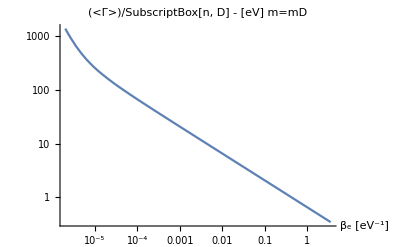

```mathematica
LogLogPlot[10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"(<Γ>)/SubscriptBox[n, D] - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

this shows the interaction rate scales as T^(1/2) near recombination

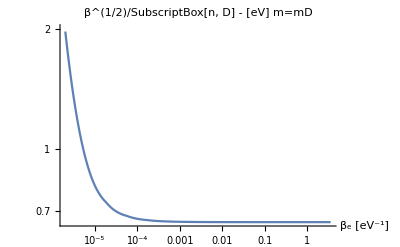

```mathematica
LogLogPlot[β^(1/2)10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(1/2)/SubscriptBox[n, D] - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,2}]
```

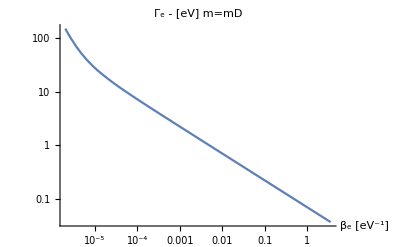

```mathematica
LogLogPlot[(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Γ_e - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

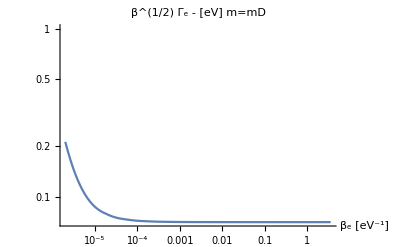

```mathematica
LogLogPlot[β^(1/2)(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(1/2) Γ_e - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,1}]
```

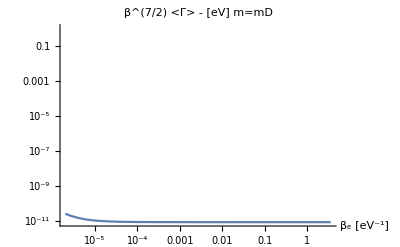

```mathematica
LogLogPlot[β^(7/2)(nD0[0.01,1000"me"/.CosmoParams[]](1/(β "T0"))^3/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(7/2) <Γ> - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,1}]
```

Now compute ((Γ̄)_e)/H

```mathematica
(*H=1/(10^28 eV β^2)*)
ΓebarbyH=1/(H[β]/.CosmoParams[])(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]]/.β->(1/("TR")/.CosmoParams[])
```

1.03254×10^27

```mathematica
ϵmax = √(r/ΓebarbyH)/.r->10^-4
```

3.11205×10^-16

This is much too stringent. Now compute (n_e(Γ̄)_e)/H

```mathematica
(*H=1/(10^28 eV β^2)*)
ΓebarbyH=1/(H[β]/.CosmoParams[])(nD0[0.01,1000"me"/.CosmoParams[]](1/(β "T0"))^3/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]]/.β->(1/("TR")/.CosmoParams[])
```

2.71448×10^15

```mathematica
ϵmax = √(r/ΓebarbyH)/.r->10^-4
```

1.91936×10^-10

```mathematica
"n0"(("TR")/("T0"))^3/.CosmoParams[]
```

2.62894×10^-12

```mathematica
("TR")^-3/.CosmoParams[]
```

48.0841

```mathematica
Simplify[NonNumIntegrand[m,m,κ,ξβ,ξE,0]]/."me"->m
```

(α ⅇ^-ξE κ^2 √(m/(Tdt ξβ)) (Tdt^3 m ξE ξβ (64 n0^2 α^2 m^2 π^4+12 n0 Tdt^3 α m^2 π^2 ξE ξβ+Tdt^6 m^2 ξβ^2 (ξE^2+2 ξE ξβ+2 ξβ^2))+8 n0 α m (8 n0 α m π^3+Tdt^3 m π ξE ξβ)^2 Log[(8 n0 α m π^2)/(Tdt^3 ξβ^2)]-8 n0 α m (8 n0 α m π^3+Tdt^3 m π ξE ξβ)^2 Log[(8 n0 α m π^2+Tdt^3 m ξE ξβ)/(Tdt^3 ξβ^2)]))/(2 g pth^3 Tdt^4 m π^3 ξβ^3 (8 n0 α m π^2+Tdt^3 m ξE ξβ))

```mathematica
?NonNumIntegrand
```